# Midiendo la ergodicidad de nuevo

Acá se medirá de nuevo la ergodicidad, pero para las preimágenes generadas con la implementación correcta.

```mathematica
Get["/media/storage/ciencia/investigacion/tesis/codigos-tesis/CoolTools2.m"]
Get["/media/storage/ciencia/investigacion/tesis/codigos-tesis/usefulFunctions.wl"]
<<"MaTeX`"
```

```mathematica
enes = {10000, 20000, 40000, 60000, 80000, 100000, 200000, 350000, 500000};
deltas = {0.005, 0.01, 0.03, 0.05, 0.07, 0.1};
betas = {100, 250, 400, 600, 750, 1000};
```

## Importando datos

Los vectores de mínimas distancias ya fueron generados en el cluster. Acá se importarán

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/tesis/mh_muestras_GOOD/distintas_Nbetasydeltas_Rp5Pp3_DOS/minvecs"]
```

/media/storage/ciencia/investigacion/tesis/mh_muestras_GOOD/distintas_Nbetasydeltas_Rp5Pp3_DOS/minvecs

```mathematica
minVecsδ1 = Get["minVecs_beta="<>ToString[#]<>"_delta=0.005_rz=0.5_p=0.3_allN.wl"]& /@ betas;
minVecsδ2 = Get["minVecs_beta="<>ToString[#]<>"_delta=0.01_rz=0.5_p=0.3_allN.wl"]& /@ betas;
minVecsδ3 = Get["minVecs_beta="<>ToString[#]<>"_delta=0.03_rz=0.5_p=0.3_allN.wl"]& /@ betas;
minVecsδ4 = Get["minVecs_beta="<>ToString[#]<>"_delta=0.05_rz=0.5_p=0.3_allN.wl"]& /@ betas;
minVecsδ5 = Get["minVecs_beta="<>ToString[#]<>"_delta=0.07_rz=0.5_p=0.3_allN.wl"]& /@ betas;
minVecsδ6 = Get["minVecs_beta="<>ToString[#]<>"_delta=0.1_rz=0.5_p=0.3_allN.wl"]& /@ betas;
```

De una vez calculamos aquí las ergodicidades

```mathematica
ergsδ1 = Map[Map[ergodicityMeasure2[#]&, #]&, minVecsδ1]//Transpose;
ergsδ2 = Map[Map[ergodicityMeasure2[#]&, #]&, minVecsδ2]//Transpose;
ergsδ3 = Map[Map[ergodicityMeasure2[#]&, #]&, minVecsδ3]//Transpose;
ergsδ4 = Map[Map[ergodicityMeasure2[#]&, #]&, minVecsδ4]//Transpose;
ergsδ5 = Map[Map[ergodicityMeasure2[#]&, #]&, minVecsδ5]//Transpose;
ergsδ6 = Map[Map[ergodicityMeasure2[#]&, #]&, minVecsδ6]//Transpose;
```

```mathematica
(*arreglando los datos para graficar*)
ergDataδ1 = Map[MapThread[{#1, #2}&, {betas, #}]&, ergsδ1];
ergDataδ2 = Map[MapThread[{#1, #2}&, {betas, #}]&, ergsδ2];
ergDataδ3 = Map[MapThread[{#1, #2}&, {betas, #}]&, ergsδ3];
ergDataδ4 = Map[MapThread[{#1, #2}&, {betas, #}]&, ergsδ4];
ergDataδ5 = Map[MapThread[{#1, #2}&, {betas, #}]&, ergsδ5];
ergDataδ6 = Map[MapThread[{#1, #2}&, {betas, #}]&, ergsδ6];
```

```mathematica
ergsδ1//Transpose
```

{{0.846042,0.831171,0.528921,0.615725,0.401935,0.493141,0.352426,0.390014,0.21176},{0.903064,0.7664,0.791212,0.571715,0.63123,0.610686,0.487471,0.219999,0.199091},{0.972065,0.952471,0.705593,0.740316,0.572874,0.697237,0.41489,0.275847,0.294712},{0.958278,0.870199,0.791609,0.765974,0.737998,0.771498,0.616765,0.375446,0.327562},{0.998468,0.932486,0.895915,0.761901,0.64811,0.530433,0.638623,0.43587,0.338179},{1.0407,0.953542,0.895676,0.802718,0.818104,0.655417,0.583446,0.431887,0.457709}}

```mathematica
(*datos en función de N*)
ergDataδ1n = MapThread[{#1, #2}&, {enes, #}]& /@ Transpose[ergsδ1];
ergDataδ2n = MapThread[{#1, #2}&, {enes, #}]& /@ Transpose[ergsδ2];
ergDataδ3n = MapThread[{#1, #2}&, {enes, #}]& /@ Transpose[ergsδ3];
ergDataδ4n = MapThread[{#1, #2}&, {enes, #}]& /@ Transpose[ergsδ4];
ergDataδ5n = MapThread[{#1, #2}&, {enes, #}]& /@ Transpose[ergsδ5];
ergDataδ6n = MapThread[{#1, #2}&, {enes, #}]& /@ Transpose[ergsδ6];
```

## Graficando los datos

### Ergodicidad vs Beta

```mathematica
colors=(("DefaultPlotStyle"/.(Method /. 
     Charting`ResolvePlotTheme["Scientific" ,  ListLogLogPlot]))/. Directive[x_,__]:>x)
```

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

```mathematica
legend = LineLegend[colors, MaTeX[{"10\\,000", "20\\,000", "40\\,000", "60\\,000","80\\,000", "10^5", "2\\times 10^5", "3.5\\times 10^5", "5\\times 10^5"}], 
				 LegendLabel->MaTeX["N", Preamble->{"\\usepackage{newtxmath}"}], LegendFunction->(Framed[#1, FrameStyle->LightGray] & )];
```

```mathematica
data = {ergDataδ1, ergDataδ2, ergDataδ3, ergDataδ4, ergDataδ5, ergDataδ6};
```

```mathematica
plotsErgVSbeta = MapThread[Show[ListLogLogPlot[#1, PlotLabel->MaTeX["\\delta = "<>ToString[#2], Preamble->{"\\usepackage{newtxmath}"}], 
				                PlotTheme->"Scientific",
				                PlotRange->{0.04, 1.2},
				                Joined->True, Mesh->All, MeshStyle->PointSize[0.014], GridLines->Automatic, 
				                FrameStyle->Black,
				                FrameLabel->MaTeX[{"\\text{Estrechez}\\,\\,(\\beta)", "E_1"}, Preamble->{"\\usepackage{newtxmath}"}]],
		    	               LogLogPlot[0.1, {x,0,1000}, PlotStyle->{Red,Dashed}]]&, 
		                  {data, deltas}];
```

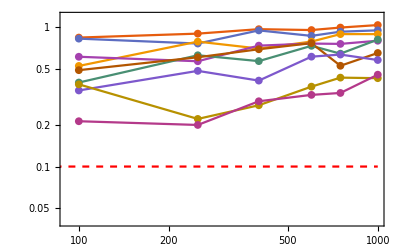
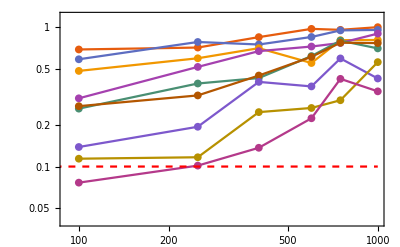
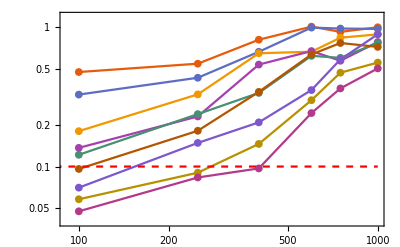
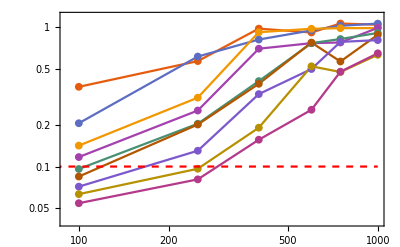
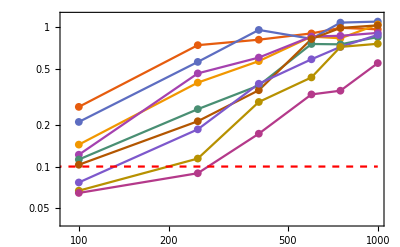
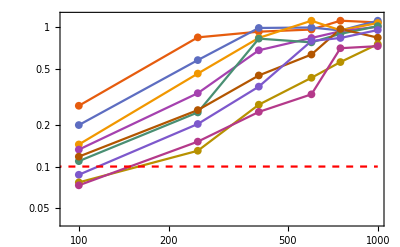
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- |

```mathematica
Grid[{plotsErgVSbeta[[1;;2]]~Join~{Item[legend, Alignment->Center]},
	  plotsErgVSbeta[[3;;4]]~Join~{SpanFromAbove},
	  plotsErgVSbeta[[5;;]]~Join~{SpanFromAbove}
}, ItemStyle->ImageSizeMultipliers->1, Spacings->{1, 1}]
```

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/tesis/mh_muestras_GOOD"]
```

/media/storage/ciencia/investigacion/tesis/mh_muestras_GOOD

```mathematica
Export["ergVSBeta_distDeltasN_Rp5Pp3_3.pdf", %128]
```

ergVSBeta_distDeltasN_Rp5Pp3_3.pdf

### Ergodicidad vs N

```mathematica
(*Gráficas en función e N*)
dataN = {ergDataδ1n, ergDataδ2n, ergDataδ3n, ergDataδ4n, ergDataδ5n, ergDataδ6n};
```

```mathematica
legend2 = LineLegend[colors, MaTeX[betas], 
				 LegendLabel->MaTeX["\\beta", Preamble->{"\\usepackage{newtxmath}"}]];
```

```mathematica
plotsErgVSn = MapThread[Show[ListLogLogPlot[#1, PlotLabel->MaTeX["\\delta = "<>ToString[#2], Preamble->{"\\usepackage{newtxmath}"}], 
				                PlotTheme->"Scientific",
				                PlotRange->{0.04, 1.2},
				                Joined->True, Mesh->All, MeshStyle->PointSize[0.014], GridLines->Automatic, 
				                FrameStyle->Black,
				                FrameLabel->MaTeX[{"\\text{Iteraciones}\\,\\,(N)", "E_1"}, Preamble->{"\\usepackage{newtxmath}"}]],
		    	               LogLogPlot[0.1, {x,0,500000}, PlotStyle->{Red,Dashed}]]&, 
		                  {dataN, deltas}];
```

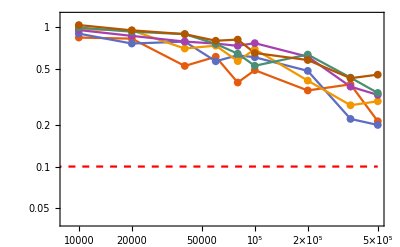
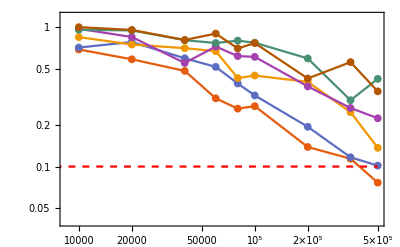
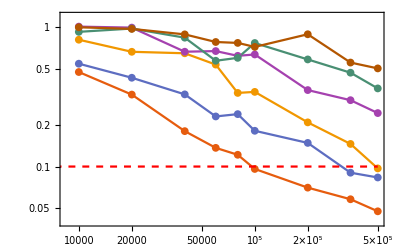
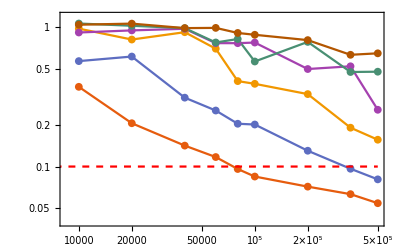
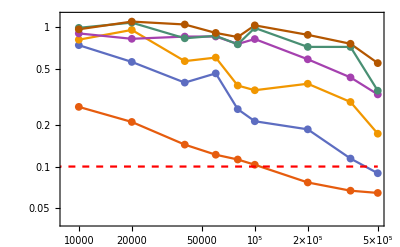
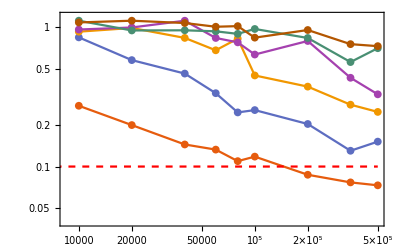
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- |

```mathematica
Grid[{plotsErgVSn[[1;;2]]~Join~{legend2},
	  plotsErgVSn[[3;;4]]~Join~{legend2},
	  plotsErgVSn[[5;;]]~Join~{legend2}
}, ItemStyle->ImageSizeMultipliers->1, Spacings->{1, 1}]
```

```mathematica
Export["ergVSn_distDeltasBetas_Rp5Pp3.pdf", %174]
```

ergVSn_distDeltasBetas_Rp5Pp3.pdf